0.0634954 (2+Cos[t]-Sin[t]+t Sin[t]^2+Sin[t]^5)

{9.11169,10.1142,11.1364,5.57763,4.2459,12.8708,21.9434}

75.

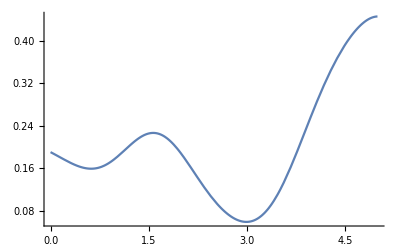

```mathematica
T=RandomInteger[{1,10}];
rounds =7;
stake = 75;
f[x_] = (x*Sin[x]^2+D[Cos[x],{x,T}]+D[Sin[x],{x,T}]+Sin[x]^T+2);
F[x_] = f[t]/NIntegrate[f[t],{t,0,T}];
F[x]
S = Table[stake*NIntegrate[F[t],{t,i*T/rounds,(i+1)*T/rounds}],{i,0,rounds-1}]
Sum[Part[S,i],{i,1,rounds}]
Plot[F[t],{t,0,T},PlotRange->Full ]
```

```mathematica
Manipulate[Plot[{1+(ffail^2/s)^2,h},{s,0,1000},PlotRange->{{0,300},{0,36}},AxesLabel->"Reps vs. Stake"],{ffail,1,100,1},{h,0,36,1}]
```

```mathematica
Manipulate[Plot[{fail^2/(d-1)^(.5),k},{d,0,30},PlotRange->{{0,30},{0,300}},AxesLabel->"Stake vs. Reps"],{fail,1,100,1},{k,0,300,1}]
```

```mathematica
"Hypothesis: a (or b) is actually the failure rate, given (s,d)... weird."
```

```mathematica
Clear[D];
```

```mathematica
Plot3D[.01*B^(1/2)(D-1)^(1/4),{B,0,300},{D,0,30},PlotRange->{0,.5},AxesLabel->Failure]
```

-Graphics3D-

```mathematica
Manipulate[Plot[{l/(2-l),g},{l,0.01,1},PlotRange->{{0,.3},{0,.2}}],{g,0,.2,.01}]
```

```mathematica
Manipulate[Plot[{( B^(3/2)(d-1)^(1/4))/(200-B^(1/2)(d-1)^(1/4)),h},{B,1,500},PlotRange->{{0,100},{0,20}},AxesLabel->"Rev Per Cust vs. buyin"],{d,1,60,1},{h,0,100,.1}]
```

```mathematica
Manipulate[Plot[(Buyin^(1/2)(d-1)^(1/4))/(200-Buyin^(1/2)(d-1)^(1/4)),{Buyin,1,300},PlotRange->{{0,300},{0,.3}},AxesLabel->"user profit % vs. buyin"],{d,1,60,1}]
```